```mathematica
β=1000;
L=1.;
yL=0.5;
ds = 0.01;
```

```mathematica
Clear[x,y,α,F]
res=NDSolve[{
F'[s]==Sin[α[s]]-β x[s] Cos[α[s]],
α'[s]==1/F[s] (Cos[α[s]]+β x[s] Sin[α[s]]),
x'[s]==Cos[α[s]],y'[s]==Sin[α[s]],
x[0]==0,y[0]==0,
x[L]==0,y[L]==yL
},{F,α,x,y},{s,0,L},Method->"Shooting"];
{xr[s_],yr[s_],αr[s_],Fr[s_]}={x[s],y[s],α[s],F[s]}/.res[[1]];
```

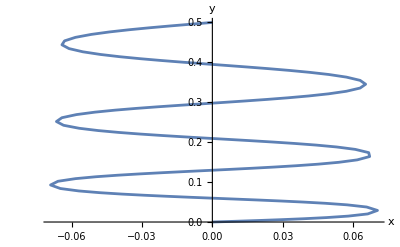

```mathematica
ListLinePlot[Table[{xr[s],yr[s]},{s,0,L,ds}],PlotRange->All,AxesLabel->{"x","y"}]
```